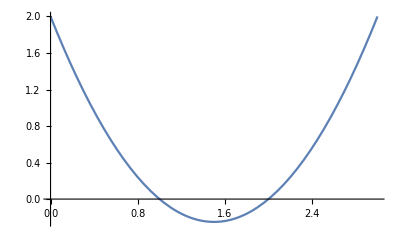

```mathematica
Plot[(x-1) (x-2),{x,0,3}]
```

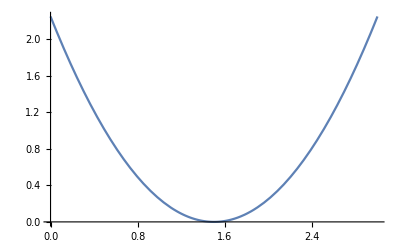

```mathematica
Plot[(x- 1.5) (x-1.5),{x,0,3}]
```

```mathematica
Plot[(x- 1 Sqrt[-1]) (x-3 Sqrt[-1]),{x,0,3}]
```

-Graphics-

```mathematica
f = a x^2+b x+c
df = D[f,x]
```

c+b x+a x^2

b+2 a x

```mathematica
Solve[(df/.x->3/2)==0]
```

{{b→-3 a}}

```mathematica
fm=Simplify[f/.{x->3/2} ]
```

(9 a)/4+(3 b)/2+c

```mathematica
Solve[(fm/.{b->-3 a})==1/4]
```

{{c→1/4+(9 a)/4}}

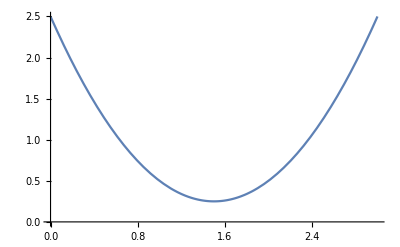

```mathematica
Plot[(a x^2+b x+c)/.{b->-3 a}/.{c->1/4+(9 a)/4}/.{a->1},{x,0,3}]
```

```mathematica
(a x^2+b x+c)/.{b->-3 a}/.{c->1/4+(9 a)/4}/.{a->1}
```

5/2-3 x+x^2